```mathematica
ImportExperimentalSubTrajectories[CSVFilePath_, cellIndeces_ ]:=(

XRecords=  Import[CSVFilePath,"CSV"][[2;;]];
XPerCell = SplitBy[{#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[1]],#[[2]]}& /@ XRecords, First ];

cellRecords = Table[(
cellIndex= XPerCell[[ii,1,-1]];
cellName =  XPerCell[[ii,1,1]];
Table[(
age0= XPerCell[[ii,jj,2]];
x0= XPerCell[[ii,jj,3]];
age1 = XPerCell[[ii,jj+1,2]];
x1= XPerCell[[ii,jj+1,3]];
s0=XPerCell[[ii,jj,4]];
s1=XPerCell[[ii,jj+1,4]];
Xrecordi = XPerCell[[ii,jj,6]];
<|"cell_name"->cellName, "Xi"->Xrecordi, 
"age"->age0, "X(age)"->x0,"s(age)"->s0,
"next_age"-> age1, "X(next_age)"->x1, "s(next_age)"->s1|>
),{jj,Range[1, Length[ XPerCell[[ii]] ]-1 ]}]
),{ii,cellIndeces}];

cellRecords=SortBy[Catenate[cellRecords],#[["Xi"]]&];
GroupBy[cellRecords,#[["cell_name"]]&]
);

BASEDIR="/Users/yyfwuhan/Public/Box Sync/2019-AlonLab-PI-data-variations/MP-SR likelihood/";
cellRecords=ImportExperimentalSubTrajectories[FileNameJoin[
{BASEDIR,
"EstimatedDamage_wt_ws7d0.csv"}
],Range[648]];
SampleIndsPartitions=Get[FileNameJoin[{BASEDIR,"EstimatedDamage_wt_ws7d0_sampleIndsPartitions41.wl"}]];
SampleNames=Keys[cellRecords];
XsCount = Length[cellRecords[[#]]]&/@SampleNames;
LLdata1=Get[#] &/@FileNames["*.nb", FileNameJoin[{BASEDIR, "productionMPSR/stochMP_24th"}]];
LLdata2=Get[#] &/@FileNames["*.nb", FileNameJoin[{BASEDIR, "productionMPSR/stochMP_24thb"}]];
```

```mathematica
LLdata=Join[LLdata1,LLdata2];
```

```mathematica
GetMeanScorePerCell[cellScores_]:= 
Mean[ToExpression[#]&/@cellScores[[2]]];
GetSampleIs[data_]:=#[[1]]&/@data[[2]];
dataSampleIs = If[AllTrue[LLdata, (GetSampleIs[#]==GetSampleIs[LLdata[[1]]])&],GetSampleIs[LLdata[[1]]],{}];
LLdataTransformed ={#[[1]],GetMeanScorePerCell/@#[[2]]}&/@LLdata;
```

```mathematica
BScellN = Round[Length[dataSampleIs]];
SampleIs = RandomInteger[{1,Length[dataSampleIs]},{1000,BScellN}];
LLScorePerBS[LLScoresPerCell_,SampleIndeces_]:=(
CellScoreByBS =Map[LLScoresPerCell[[#]]*(XsCount[[#]]-1)&,SampleIndeces,{2}];
XsCountByBS =Map[(XsCount[[#]]-1)&,SampleIndeces,{2}];
Total[CellScoreByBS,{2}]/Total[XsCountByBS,{2}]
 )
MeanBSLLscores={LLdataTransformed[[#,1]], LLScorePerBS[LLdataTransformed[[#,2]],SampleIs]}&/@Range[Length[LLdataTransformed]];
(*LLScorePerBS[LLScores_, SampleIndeces_]:=
Mean[Catenate[#]]&/@(Map[LLScores[[dPIsLeftInd[[#]];;dPIsRightInd[[#]]]]&,SampleIndeces,{2}])
Timing[MeanBSLLscores={#[[1]], LLScorePerBS[#[[2]],SampleIs]}&/@LLdataTransformed;]*)
LLscoreTopInd[BSi_]:=TakeLargestBy[Range[Length[LLdataTransformed]],MeanBSLLscores[[#, 2, BSi]]&, 3];
LLscoreTopInds = LLscoreTopInd[#]&/@Range[Length[SampleIs]];
```

```mathematica
TopRankedParsDF=#[[1,{1,2,3,4,5,6},2]]&/@(MeanBSLLscores[[#[[1]]&/@LLscoreTopInds]]);
parsTransform[pars_]:={
pars[[1]]/0.0044, (*t3 = beta/eta [hour]*)
pars[[2]]/0.8,
pars[[3]]/0.154,(*q0 = beta/eps/a [1]*)
pars[[4]]/0.5,
Exp[pars[[5]]],
pars[[6]]/pars[[2]]}
TopRankedTransParsDF =parsTransform[#]&/@TopRankedParsDF;
```

```mathematica
N[{Mean[TopRankedTransParsDF], StandardDeviation[TopRankedTransParsDF
]}]//MatrixForm
N[Correlation[TopRankedTransParsDF]]//MatrixForm
N[parsTransform[MeanBSLLscores[[#,1,{1,2,3,4,5,6},2]]]&/@ (#[[1]]&/@LLscoreTopInds[[;;25]])]//MatrixForm
{Mean[MeanBSLLscores[[Commonest[#[[1]]&/@LLscoreTopInds][[1]],2]]],StandardDeviation[MeanBSLLscores[[Commonest[#[[1]]&/@LLscoreTopInds][[1]],2]]],parsTransform[MeanBSLLscores[[Commonest[#[[1]]&/@LLscoreTopInds][[1]],1,{1,2,3,4,5,6},2]]]}
```

(1.1528 | 1.40156 | 1.02196 | 0.66368 | 1.3335 | 0.31815
0.0602378 | 0.108368 | 0.0370071 | 0.0573773 | 0.100662 | 0.0170108)

(1. | 0.394893 | 0.260311 | 0.231027 | 0.248811 | -0.242579
0.394893 | 1. | 0.027891 | -0.715451 | 0.0895731 | 0.714539
0.260311 | 0.027891 | 1. | 0.123318 | -0.240162 | -0.138933
0.231027 | -0.715451 | 0.123318 | 1. | 0.0554459 | -0.846302
0.248811 | 0.0895731 | -0.240162 | 0.0554459 | 1. | -0.216017
-0.242579 | 0.714539 | -0.138933 | -0.846302 | -0.216017 | 1.)

(1.14 | 1.38 | 1.02 | 0.66 | 1.29 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.44 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.365 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.29 | 0.32
1.14 | 1.16 | 1.02 | 0.82 | 1.365 | 0.27
1.14 | 1.38 | 1.02 | 0.66 | 1.44 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.14 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.44 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.29 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.365 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.29 | 0.32
1.3 | 1.6 | 1.02 | 0.66 | 1.44 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.44 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.44 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.29 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.29 | 0.32
1.14 | 1.16 | 1.02 | 0.82 | 1.365 | 0.27
1.14 | 1.38 | 1.02 | 0.66 | 1.44 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.14 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.215 | 0.32
0.98 | 1.6 | 1.02 | 0.5 | 1.215 | 0.37
1.14 | 1.38 | 1.02 | 0.66 | 1.14 | 0.32
1.14 | 1.16 | 1.02 | 0.82 | 1.365 | 0.27
1.14 | 1.38 | 1.02 | 0.66 | 1.29 | 0.32
1.14 | 1.38 | 1.02 | 0.66 | 1.44 | 0.32)

{-2.06441,0.0136479,{1.14,1.38,1.02,0.66,1.29,0.32}}

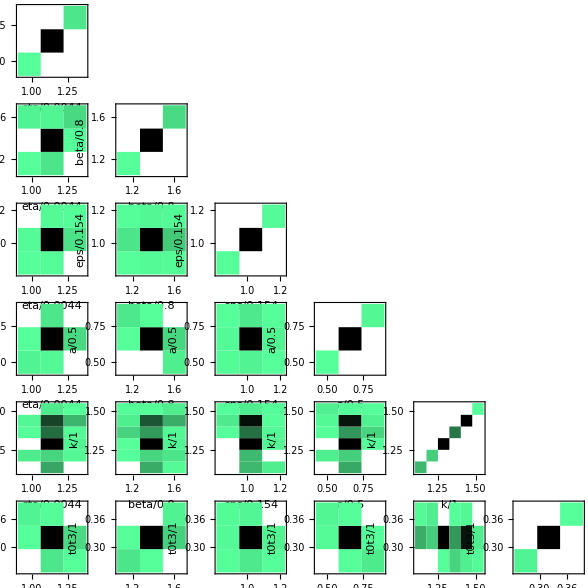

```mathematica
parTransRange={
eta-> {.98,1.3,.16},
beta->{1.16,1.6,.22},
eps-> {.88,1.16,.14},
a->{.5,.82,.16},
k->{1.14,1.515,0.075},
t0t3->{.27,.37,.05}
};
parTransCenter={eta->0.0044,beta->0.8,eps->0.154,a->0.5,k->1, t0t3->1};
GraphicsGrid[Table[Table[
DensityHistogram[N[{#[[i]],#[[j]]}]&/@TopRankedTransParsDF,
			{({#[[1]]-#[[3]]/2,#[[2]]+#[[3]]/2,#[[3]]}&)[parTransRange[[i,2]]],
			({#[[1]]-#[[3]]/2,#[[2]]+#[[3]]/2,#[[3]]}&)[parTransRange[[j,2]]]},
			"Probability",ColorFunction->(Hue[2/5,2/3,1-#]&),
			PlotRange->{({#[[1]]-#[[3]]/2,#[[2]]+#[[3]]/2}&)[parTransRange[[i,2]]],
					    ({#[[1]]-#[[3]]/2,#[[2]]+#[[3]]/2}&)[parTransRange[[j,2]]]},
			FrameLabel->{ToString[parTransRange[[i,1]]]<>"/"<>ToString[parTransCenter[[i,2]]],
					       ToString[parTransRange[[j,1]]]<>"/"<>ToString[parTransCenter[[j,2]]]}
			(*,Gridlines->{Range@@parTransRange[[i,2]],Range@@parTransRange[[j,2]]}*)
]
,{i,1,j}],{j,1,6}]]
```

```mathematica
Table[Flatten[{i,Mean[MeanBSLLscores[[i,2]]],StandardDeviation[MeanBSLLscores[[i,2]]],parsTransform[MeanBSLLscores[[i,1,{1,2,3,4,5,6},2]]]}],{i,Commonest[#[[1]]&/@LLscoreTopInds,5]}]//MatrixForm
```

(249 | -2.06441 | 0.0136479 | 1.14 | 1.38 | 1.02 | 0.66 | 1.29 | 0.32
606 | -2.06462 | 0.0133838 | 1.14 | 1.38 | 1.02 | 0.66 | 1.44 | 0.32
854 | -2.06511 | 0.0137078 | 1.14 | 1.38 | 1.02 | 0.66 | 1.365 | 0.32
201 | -2.06603 | 0.0141625 | 1.14 | 1.38 | 1.02 | 0.66 | 1.14 | 0.32
532 | -2.06574 | 0.0134175 | 1.3 | 1.6 | 1.02 | 0.66 | 1.44 | 0.32)

```mathematica
parsTransform[LLdataTransformed[[249,1,{1,2,3,4,5,6},2]]]
```

{1.14,1.38,1.02,0.66,1.29,0.32}

```mathematica
Select[LLdataTransformed[[249,2]],#<-Log[2000/50*100.]&]
```

{}